# PlotFunctions

## Tyson Jones tyson.jones@monash.edu June 2017

## Paclets Test

```mathematica
Clear["Global`*"]
```

## Import

```mathematica
PacletDirectoryAdd[NotebookDirectory[]];
```

```mathematica
<< PlotFunctions`
```

## Two Dimensions

## Functional Plots

```mathematica
PlotWavefunction[
	Function[{x, y}, Sin[x] Sin[y]^2 Exp[-ⅈ x + ⅈ y]], {-3, 3}, {-3, 3},
	Potential -> ((#1^2+ #2^2)/9 &)
]
```

-Graphics3D-

```mathematica
PlotWavefunction[
	(Exp[-#^2] Exp[ⅈ #] &), 
	{ -2, 2}, {-3, 3}
]
```

-Graphics3D-

```mathematica
PlotWavefunction[
	(Exp[-#1^2] Exp[-2 #2^10] Exp[Tanh[#2/#1] ⅈ] &), 
	{ -2, 2}, {-3, 3},
	Potential -> Function[{x, y}, x y]
]
```

-Graphics3D-

## Symbolic Plots

coming soon!

## Interpolating Function Plots

coming soon!

## List Plots

coming soon!

## Number Plots

coming soon!

## Efficiency Tests

```mathematica
Manipulate[
	PlotWavefunction[
		Function[{x, y}, Sin[x t] Sin[y]^2 Exp[-ⅈ x + ⅈ t y]], {-3, 3}, {-3, 3},
		Potential -> ((#1^2+ #2^2)/9 &),
		ShowBar -> False,
		PointsActivePassive -> {30, 50}
	],
	{t, 1, 10},
	SaveDefinitions->True
]
```

```mathematica
Manipulate[
	PlotWavefunction[
		Function[{x, y}, Sin[x t] Sin[y]^2 Exp[-ⅈ x + ⅈ t y]], {-3, 3}, {-3, 3},
		Potential -> ((#1^2+ #2^2)/9 &),
		ShowBar -> False,
		PointsActivePassive -> {10, 50}
	],
	{t, 1, 10}
]
```

## One Dimension

## Symbolic Plots

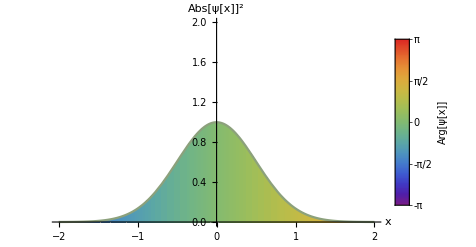

```mathematica
PlotWavefunction[
	Exp[-x^2] Exp[ⅈ x], 
	{x, -2, 2},
	PlotRange -> {0, 2}
]
```

```mathematica
a
```

a

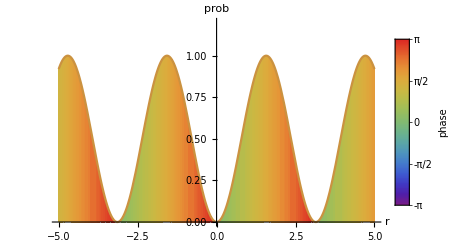

```mathematica
PlotWavefunction[
	Sin[x]Exp[ⅈ x], 
	{x, -5, 5},
	PlotRange -> {0, 1.2},
	Labels -> {r, prob, phase}
]
```

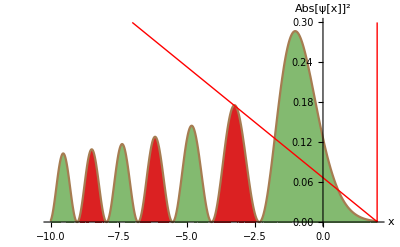

```mathematica
PlotWavefunction[
	AiryAi[x], 
	{x, -10, 2},
	PlotRange -> {0, 0.3},
	Potential -> - (x-2)/30 + UnitStep[x-1.99],
	PotentialFilling -> False,
	ShowBar -> False
]
```

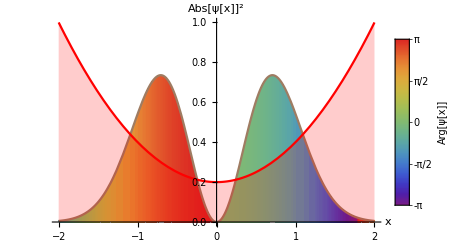

```mathematica
PlotWavefunction[
	Exp[-x^2] HermiteH[1, x] Exp[- ⅈ x^2],
	{x, -2, 2},
	Potential ->x^2,
	PotentialTransform -> (#/5 + 0.2&)
]
```

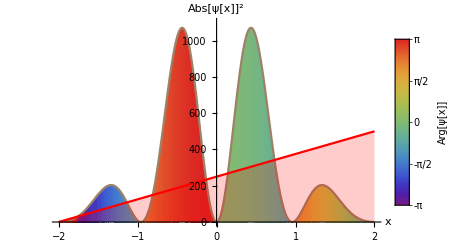

```mathematica
PlotWavefunction[
	Exp[-x^2] HermiteH[5, x] Exp[- ⅈ x^2],
	{x, -2, 2},
	PlotRange -> {0, 1100},
	Potential ->{0, 1, 2, 3, 4, 5},
	PotentialTransform -> (100 # &)
]
```

## Function Plots

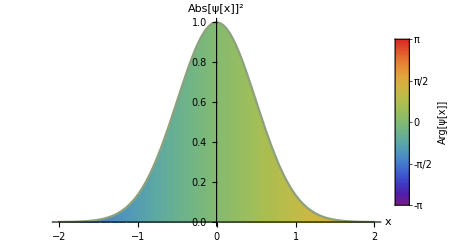

```mathematica
PlotWavefunction[
	(Exp[-#^2] Exp[ⅈ #] &), 
	{ -2, 2}
]
```

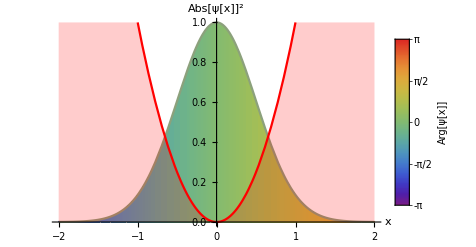

```mathematica
PlotWavefunction[
	(Exp[-#^2] Exp[ⅈ #] &), 
	{ -2, 2},
	Potential -> (#^2&)
]
```

## Interpolating Function Plots

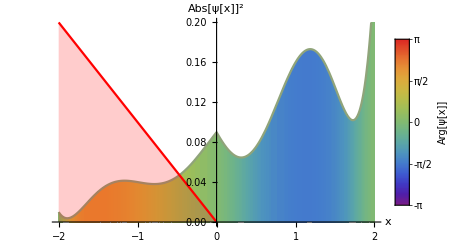

```mathematica
PlotWavefunction[
	ListInterpolation[{1, 2 ⅈ, 3, -4ⅈ, 5}/10, {{-2, 2}}], 
	{ -2, 2},
	PlotRange -> {0, 0.2},
	Potential -> (-#&),
	PotentialTransform -> (#/10&)
]
```

## List Plots

```mathematica
PlotWavefunction[
	{1, 2 ⅈ, 3, -4ⅈ, 5}/10, 
	{ -2, 2},
	PlotRange -> {0, 0.2},
	Potential -> (-#&),
	PotentialTransform -> (#/10&)
]
```

-Graphics-

## Number Plots

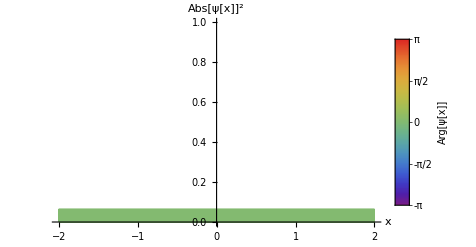

```mathematica
PlotWavefunction[
	0.25, 
	{x,  -2, 2}
]
```

```mathematica
PlotWavefunction[
	0.25, 
	{-2, 2}
]
```

-Graphics-

## Efficiency Tests

```mathematica
Manipulate[
	PlotWavefunction[
		1/(t/10+1)Exp[-(x-t)^2] Exp[ⅈ (x-t)] Exp[ⅈ t], 
		{x, -2, 6},
		ShowBar -> False
	],
	{t, 0, 4}
]
```